```mathematica
Row[Table[Hue[x],{x,0,1,0.1}]]
```

Hue[0.]Hue[0.1]Hue[0.2]Hue[0.30000000000000004]Hue[0.4]Hue[0.5]Hue[0.6000000000000001]Hue[0.7000000000000001]Hue[0.8]Hue[0.9]Hue[1.]

```mathematica
Grid[Table[x,4,5]]
```

x | x | x | x | x
x | x | x | x | x
x | x | x | x | x
x | x | x | x | x

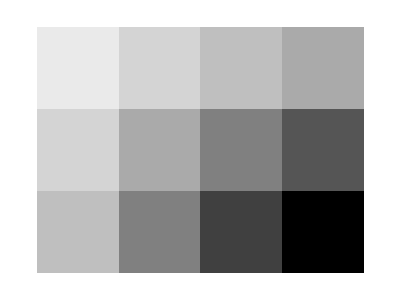

```mathematica
ArrayPlot[Table[j*i,{i,1,3},{j,1,4}]]
```

```mathematica
Table[ArrayPlot[Table[RandomInteger[1],30,30]],3,3]
```

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
ArrayPlot[ImageData[Binarize[Rasterize[Style["W",25]]]]]
```

-Graphics-

```mathematica
Rasterize[Style["W",25]]
```

-Graphics-

```mathematica
Image3D[Table[RandomInteger[1],10,10,10]]
```

-Graphics3D-

```mathematica
Grid[{{1,2},{1,2}}]
```

1 | 2
1 | 2

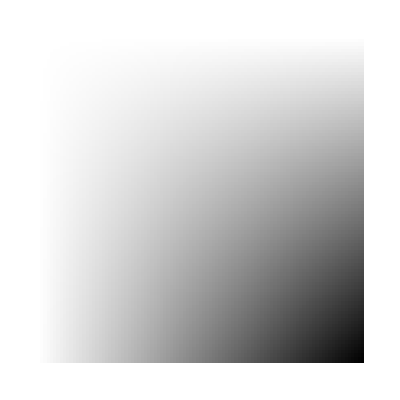

```mathematica
ArrayPlot[Table[x*y,{x,0,1,0.01},{y,0,1,0.01}]]
```

```mathematica
ArrayPlot[StringLength[Table[RomanNumeral[i*j],{i,1,100},{j,1,100}]]]
```

-Graphics-

```mathematica
Grid[Table[Style[RandomInteger[10],RandomColor[],RandomInteger[32]],10,10]]
```

1 | 8 | 10 | 1 | 8 | 7 | 4 | 9 | 1 | 4
5 | 0 | 8 | 6 | 5 | 3 | 4 | 7 | 2 | 1
6 | 9 | 9 | 5 | 4 | 0 | 9 | 6 | 4 | 7
1 | 0 | 2 | 0 | 3 | 7 | 6 | 8 | 7 | 6
9 | 9 | 4 | 4 | 1 | 2 | 4 | 2 | 3 | 2
0 | 6 | 9 | 9 | 8 | 1 | 4 | 6 | 4 | 4
4 | 5 | 8 | 0 | 4 | 7 | 10 | 5 | 5 | 0
6 | 5 | 6 | 3 | 2 | 2 | 2 | 5 | 8 | 10
0 | 10 | 7 | 3 | 5 | 1 | 1 | 3 | 4 | 0
10 | 5 | 1 | 7 | 0 | 10 | 10 | 9 | 0 | 8

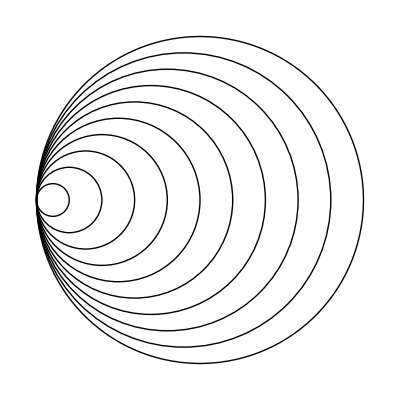

```mathematica
Graphics[Table[Circle[{x,0},x],{x,10}]]
```

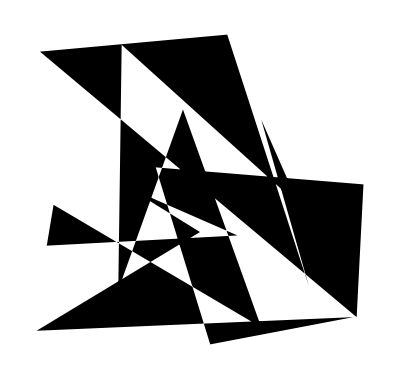

```mathematica
Graphics[Polygon[Table[RandomInteger[100],20,2]]]
```

```mathematica
Graphics3D[Table[Point[{x,y,z}],{x,10},{y,10},{z,10}],Boxed->False]
```

-Graphics3D-

```mathematica
Manipulate[Graphics3D[{Sphere[{0,0,0}],Style[Sphere[{x,0,0}],Opacity[o]]},Boxed->False],{x,1,3},{o,0.5,1}]
```

```mathematica
Graphics3D[Table[Sphere[{RandomInteger[10],RandomInteger[10],RandomInteger[10]},1],50]]
```

-Graphics3D-

```mathematica
Graphics3D[Table[Style[Sphere[{x,y,z},0.5],RGBColor[x/10,y/10,z/10]],{x,1,10},{y,1,10},{z,1,10}]]
```

-Graphics3D-

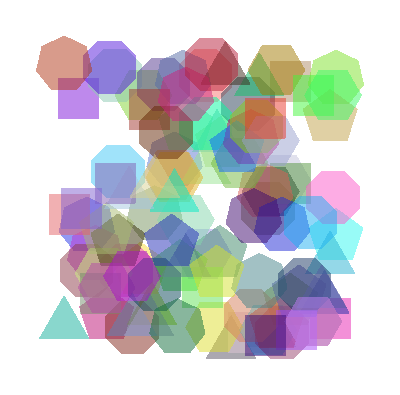

```mathematica
Graphics[Table[Style[RegularPolygon[{RandomInteger[100],RandomInteger[100]},10,RandomInteger[{3,8}]],RandomColor[],Opacity[0.5]],100]]
```

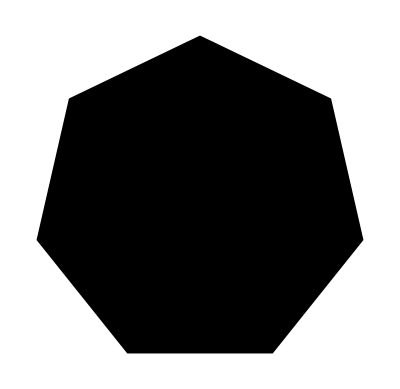

```mathematica
Graphics[RegularPolygon[{RandomInteger[100],RandomInteger[100]},10,RandomInteger[{3,8}]]]
```

```mathematica
Graphics3D[Table[Style[Point[{x,y,z}],RandomColor[]],{x,10},{y,10},{z,10}]]
```

-Graphics3D-

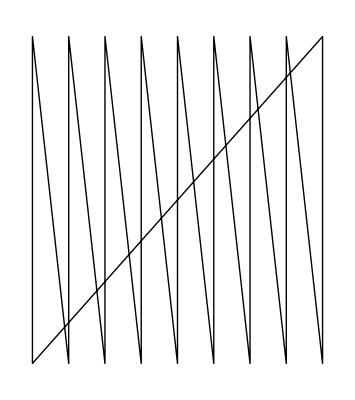

```mathematica
Graphics[Line[Table[Take[IntegerDigits[x],2],{x,10,100}]]]
```

```mathematica
Graphics3D[Line[Table[Take[IntegerDigits[x],3],{x,100,1000}]]]
```

-Graphics3D-

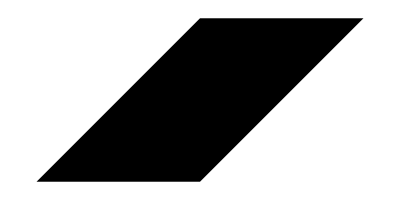

```mathematica
Graphics[Parallelogram[]]
```

```mathematica
EntityProperties[LinguisticAssistant]
```

{administrative region,alternate names,climbing difficulty,typical climbing months,continent,coordinates,country,elevation,entity classes,epoch,image,isolation,latitude,longitude,mountain range,mountain subrange,name,parent peak,position,prominence,summit reached,type}

```mathematica
UnitConvert[LinguisticAssistant["Elevation"],"Feet"]/Entity["Building","EmpireStateBuilding::h583b"]["Height"]
```

23.2231

```mathematica
DominantColors[Entity["Artwork","TheStarryNight::VincentVanGogh"]["Image"]]
```

{RGBColor[0.3332092589900391, 0.4351871320758253, 0.6023091749044202],RGBColor[0.14034730566124173, 0.1488087163233582, 0.1328080803391138],RGBColor[0.4972570418496233, 0.5560647169382823, 0.5124423328359278],RGBColor[0.7205758097128038, 0.6443860782139894, 0.1551868324905521]}

```mathematica
ColorNegate[Entity["Artwork","MonaLisa::LeonardoDaVinci"]["Image"]]
```

-Graphics-

```mathematica
Entity["GeographicRegion","Europe"]["Countries"]
```

{Albania,Andorra,Austria,Belarus,Belgium,Bosnia and Herzegovina,Bulgaria,Croatia,Czech Republic,Denmark,Estonia,Faroe Islands,Finland,France,Germany,Gibraltar,Greece,Guernsey,Hungary,Iceland,Ireland,Isle of Man,Italy,Jersey,Kosovo,Latvia,Liechtenstein,Lithuania,Luxembourg,North Macedonia,Malta,Moldova,Monaco,Montenegro,Netherlands,Norway,Poland,Portugal,Romania,Russia,San Marino,Serbia,Slovakia,Slovenia,Spain,Svalbard,Sweden,Switzerland,Ukraine,United Kingdom,Vatican City}

URLFetch::ssl: An SSL error occurred. The raw details are: "libcurl error (35): schannel: failed to receive handshake, SSL/TLS connection failed"

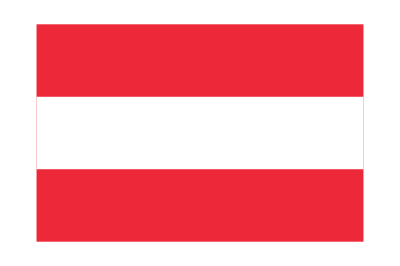
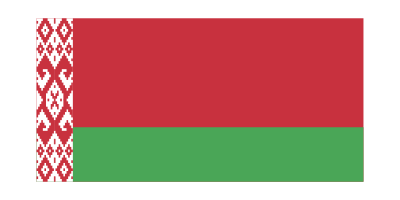
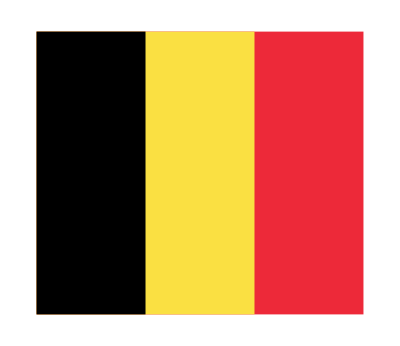
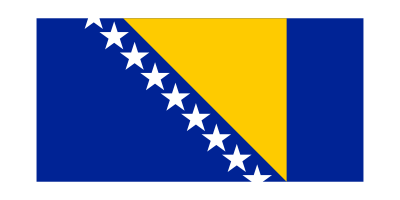
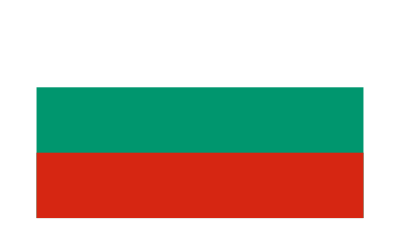
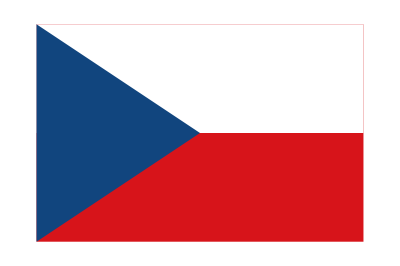
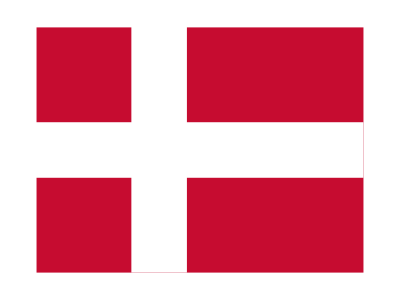
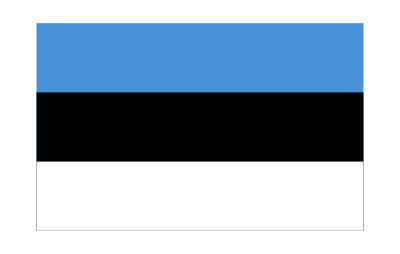


{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,Missing[RetrievalFailure],-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[a["Flag"],{a,Entity["GeographicRegion","Europe"]["Countries"]}]
```

```mathematica
UnitConvert[Quantity[2.6, "Hours"],"Seconds"]
```

9360. s

```mathematica
Quantity[45,"Meters"/"Seconds"]
```

45 m/s

```mathematica
CurrencyConvert[Quantity[2500, "Yen"],"USDollars"]
```

23.75 $

```mathematica
Rotate["Hello",Quantity[45, "AngularDegrees"]]
```

Hello

```mathematica
Rotate["Hello",45°]
```

Hello

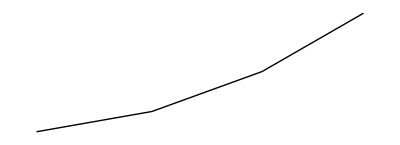

```mathematica
Graphics[Line[AnglePath[{10°,10°,10°}]]]
```

```mathematica
Rotate[-Graphics-,180°]
```

-Graphics-

```mathematica
UnitConvert[Quantity[4.3, "LightYears"],"Furlongs"]
```

2.02225×10^14 furlongs

```mathematica
PolyhedronData["Dodecahedron"]
```

-Graphics3D-

```mathematica
PolyhedronData["Dodecahedron","Image"]
```

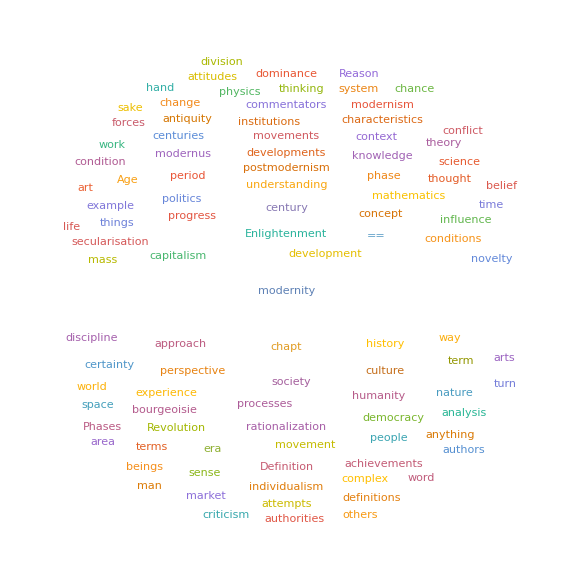

```mathematica
WordCloud[TextCases[WikipediaData["modernity"],"Noun"]]
```

```mathematica
WikipediaData["modernity"]
```

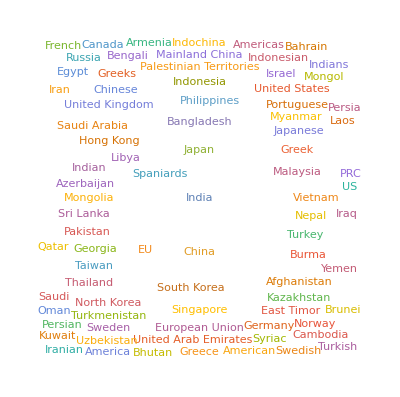

```mathematica
WordCloud[TextCases[WikipediaData["Asia"],"Country"]]
```

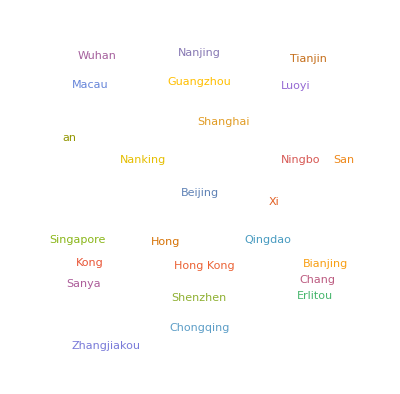

```mathematica
WordCloud[TextCases[WikipediaData["China"],"City"]]
```

```mathematica
TextStructure["You can do so much with the Wolfram Language."]
```

You
Pronoun
Noun Phrase  can
Verb  do
Verb  so
Adverbmuch
Adverb
Adverb Phrase  with
Preposition  the
DeterminerWolfram
Proper NounLanguage
Proper Noun
Noun Phrase
Prepositional Phrase
Verb Phrase
Verb Phrase.
Punctuation
Sentence